```mathematica
(*definizioni mie*)

(* FORSE MANCANO DEI MEZZI sommando sulle polarizzazioni?  NO!*)
```

```mathematica
μPDFpart[WmT,Q_]=(μPDFpart[Wmp,Q][#]+ μPDFpart[Wmm,Q][#])/1&
μPDFpart[WpT,Q_]=(μPDFpart[Wpp,Q][#]+ μPDFpart[Wpm,Q][#])/1&
μPDFpart[ZT,Q_]=(μPDFpart[Zp,Q][#]+ μPDFpart[Zm,Q][#])/1&
μPDFpart[γ,Q_]=(μPDFpart[γp,Q][#]+ μPDFpart[γm,Q][#])/1&

μbPDFpart[WmT,Q_]=(μbPDFpart[Wmp,Q][#]+ μbPDFpart[Wmm,Q][#])/1&
μbPDFpart[WpT,Q_]=(μbPDFpart[Wpp,Q][#]+ μbPDFpart[Wpm,Q][#])/1&
μbPDFpart[ZT,Q_]=(μbPDFpart[Zp,Q][#]+ μbPDFpart[Zm,Q][#])/1&
μbPDFpart[γ,Q_]=(μbPDFpart[γp,Q][#]+ μbPDFpart[γm,Q][#])/1&
```

(μPDFpart[Wmp,Q][#1]+μPDFpart[Wmm,Q][#1]) 1/1&

(μPDFpart[Wpp,Q][#1]+μPDFpart[Wpm,Q][#1]) 1/1&

(μPDFpart[Zp,Q][#1]+μPDFpart[Zm,Q][#1]) 1/1&

(μPDFpart[γp,Q][#1]+μPDFpart[γm,Q][#1]) 1/1&

(μbPDFpart[Wmp,Q][#1]+μbPDFpart[Wmm,Q][#1]) 1/1&

(μbPDFpart[Wpp,Q][#1]+μbPDFpart[Wpm,Q][#1]) 1/1&

(μbPDFpart[Zp,Q][#1]+μbPDFpart[Zm,Q][#1]) 1/1&

(μbPDFpart[γp,Q][#1]+μbPDFpart[γm,Q][#1]) 1/1&

```mathematica
μPDFpart[WmT,1000][0.1]
```

0.0525361

```mathematica
Qplot = 3TeV
```

3000

```mathematica
(* LA SCALA É STOT DEL COLLIDER*)
```

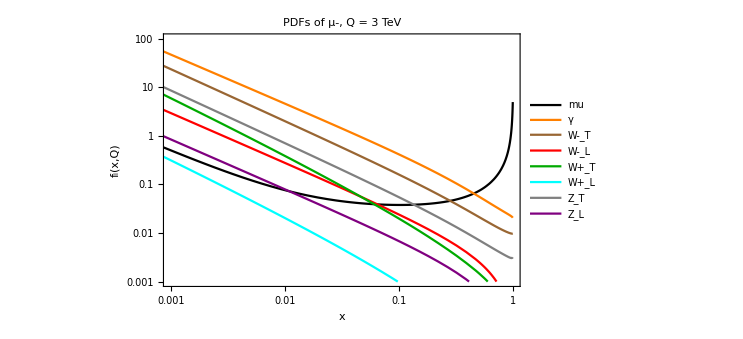

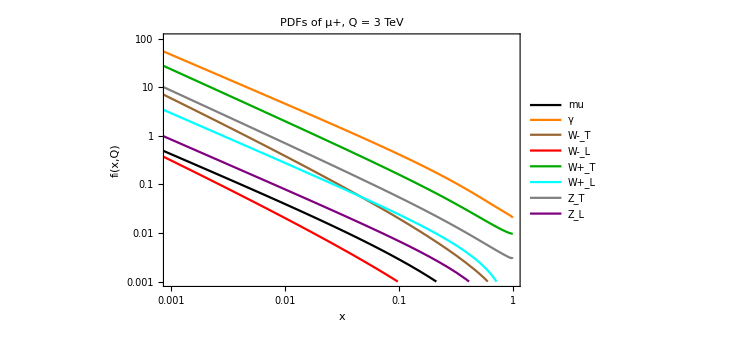

```mathematica
plotmio = LogLogPlot[{
μPDFpart[μL,Qplot][x]+μPDFpart[μR,Qplot][x],
μPDFpart[γp,Qplot][x]+ μPDFpart[γm,Qplot][x],
(*μPDFpart[gp,Qplot][x]+ μPDFpart[gm,Qplot][x],*)
μPDFpart[Wmp,Qplot][x]+ μPDFpart[Wmm,Qplot][x],μPDFpart[WmL,Qplot][x],
μPDFpart[Wpp,Qplot][x]+ μPDFpart[Wpm,Qplot][x],μPDFpart[WpL,Qplot][x],
μPDFpart[Zp,Qplot][x]+ μPDFpart[Zm,Qplot][x], μPDFpart[ZL,Qplot][x]
(*μPDFpart[νμ,Qplot][x],
 μPDFpart[νeb,Qplot][x],*)
(*μPDFpart[eL,Qplot][x]+μPDFpart[eR,Qplot][x]
qPDF[x] *)
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = "<>ToString[Qplot/1000]<>" TeV"]

plotmiomuplus = LogLogPlot[{
μbPDFpart[μL,Qplot][x]+μbPDFpart[μR,Qplot][x],
μbPDFpart[γp,Qplot][x]+ μbPDFpart[γm,Qplot][x],
(*μbPDFpart[gp,Qplot][x]+ μbPDFpart[gm,Qplot][x],*)
μbPDFpart[Wmp,Qplot][x]+ μbPDFpart[Wmm,Qplot][x],μbPDFpart[WmL,Qplot][x],
μbPDFpart[Wpp,Qplot][x]+ μbPDFpart[Wpm,Qplot][x],μbPDFpart[WpL,Qplot][x],
μbPDFpart[Zp,Qplot][x]+ μbPDFpart[Zm,Qplot][x], μbPDFpart[ZL,Qplot][x]
(*μbPDFpart[νμ,Qplot][x],
 μbPDFpart[νeb,Qplot][x],*)
(*μbPDFpart[eL,Qplot][x]+μbPDFpart[eR,Qplot][x]
qPDF[x] *)
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = "<>ToString[Qplot/1000]<>" TeV"]
```

```mathematica
(* LA SCALA É STOT DEL COLLIDER PER SQRT[X]*)
```

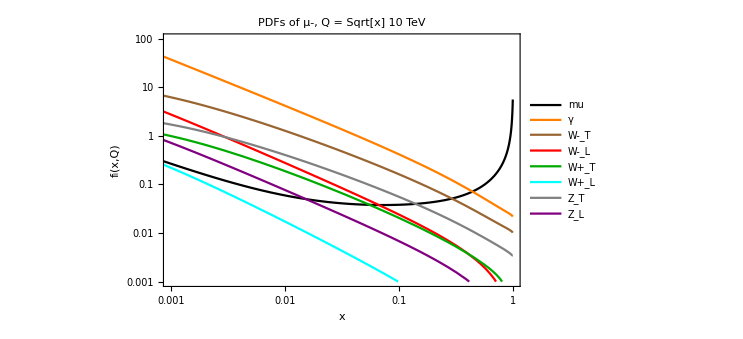

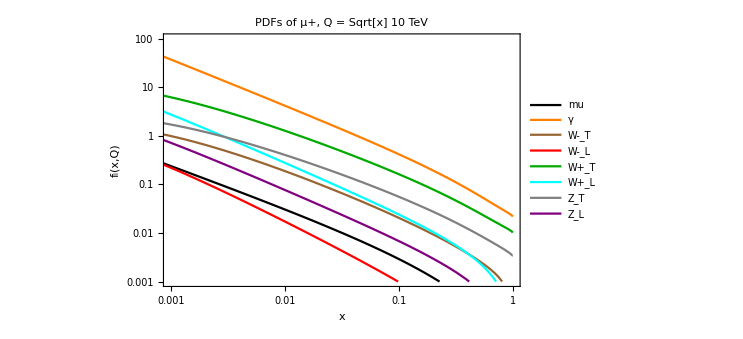

```mathematica
plotmiov2 = LogLogPlot[{
μPDFpart[μL,Qplot Sqrt[x]][x]+μPDFpart[μR,Qplot Sqrt[x]][x],
μPDFpart[γp,Qplot Sqrt[x]][x]+ μPDFpart[γm,Qplot Sqrt[x]][x],
(*μPDFpart[gp,Qplot Sqrt[x]][x]+ μPDFpart[gm,Qplot Sqrt[x]][x],*)
μPDFpart[Wmp,Qplot Sqrt[x]][x]+ μPDFpart[Wmm,Qplot Sqrt[x]][x],μPDFpart[WmL,Qplot Sqrt[x]][x],
μPDFpart[Wpp,Qplot Sqrt[x]][x]+ μPDFpart[Wpm,Qplot Sqrt[x]][x],μPDFpart[WpL,Qplot Sqrt[x]][x],
μPDFpart[Zp,Qplot Sqrt[x]][x]+ μPDFpart[Zm,Qplot Sqrt[x]][x], μPDFpart[ZL,Qplot Sqrt[x]][x]
(*μPDFpart[νμ,Qplot Sqrt[x]][x],
 μPDFpart[νeb,Qplot Sqrt[x]][x],*)
(*μPDFpart[eL,Qplot Sqrt[x]][x]+μPDFpart[eR,Qplot Sqrt[x]][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ-, Q = Sqrt[x] "<>ToString[Qplot/1000]<>" TeV"]

plotmiomuplusv2 = LogLogPlot[{
μbPDFpart[μL,Qplot Sqrt[x]][x]+μbPDFpart[μR,Qplot Sqrt[x]][x],
μbPDFpart[γp,Qplot Sqrt[x]][x]+ μbPDFpart[γm,Qplot Sqrt[x]][x],
(*μbPDFpart[gp,Qplot Sqrt[x]][x]+ μbPDFpart[gm,Qplot Sqrt[x]][x],*)
μbPDFpart[Wmp,Qplot Sqrt[x]][x]+ μbPDFpart[Wmm,Qplot Sqrt[x]][x],μbPDFpart[WmL,Qplot Sqrt[x]][x],
μbPDFpart[Wpp,Qplot Sqrt[x]][x]+ μbPDFpart[Wpm,Qplot Sqrt[x]][x],μbPDFpart[WpL,Qplot Sqrt[x]][x],
μbPDFpart[Zp,Qplot Sqrt[x]][x]+ μbPDFpart[Zm,Qplot Sqrt[x]][x], μbPDFpart[ZL,Qplot Sqrt[x]][x]
(*μbPDFpart[νμ,Qplot Sqrt[x]][x],
 μbPDFpart[νeb,Qplot Sqrt[x]][x],*)
(*μbPDFpart[eL,Qplot Sqrt[x]][x]+μbPDFpart[eR,Qplot Sqrt[x]][x]
qPDF[x]*) 
},{x,10^-4,0.9909},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta},PlotRange->{{0.00099,1},{0.001,100}},Frame->True,FrameLabel->{"x","f_i(x,Q)"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],ImageSize->550,PlotLegends->{"mu","γ","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"PDFs of μ+, Q = Sqrt[x] "<>ToString[Qplot/1000]<>" TeV"]
```

```mathematica
alpha=1/137.
(*alpha in realtà runna nelle PDF!!!!!*)
e=Sqrt[4Pi alpha]
MZ=91.1876
MW=80.379
cw=Sqrt[MW^2/MZ^2]
sw=Sqrt[1-cw^2]
g=e/sw
```

0.00729927

0.302862

91.1876

80.379

0.881469

0.472243

0.641327

```mathematica
(*gV=.
gL=.
gR=.
gt=.
MV=.*)
```

```mathematica
rulesW={(*gV->1/2*)gV->1,gL->1,gR->0,gt->g/Sqrt[2],MV->MW}

μLEVApart[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesW(*2.7 a*)
μLEVApart[Wmm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2]/.rulesW (*2.7 b*)
μLEVApart[WmL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesW(*2.7 c*)

μREVApart[Wmp,Q_,x_]:=(gR^2/gL^2) μLEVApart[Wmm,Q,x] /.rulesW(*2.7 d*)
μREVApart[Wmm,Q_,x_]:=(gR^2/gL^2) μLEVApart[Wmp,Q,x] /.rulesW(*2.7 e*)
μREVApart[WmL,Q_,x_]:=(gR^2/gL^2) μLEVApart[WmL,Q,x] /.rulesW(*2.7 f*)


μEVApart[Wmp,Q_,x_]:=(μLEVApart[Wmp,Q,x]+μREVApart[Wmp,Q,x])/2
μEVApart[Wmm,Q_,x_]:=(μLEVApart[Wmm,Q,x]+μREVApart[Wmm,Q,x])/2
μEVApart[WmL,Q_,x_]:=(μLEVApart[WmL,Q,x]+μREVApart[WmL,Q,x])/2


(*Scale as LEPDF EVA*)

μLEVApartv2[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesW(*2.7 a*)
μLEVApartv2[Wmm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesW (*2.7 b*)
μLEVApartv2[WmL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesW(*2.7 c*)

μREVApartv2[Wmp,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[Wmm,Q,x] /.rulesW(*2.7 d*)
μREVApartv2[Wmm,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[Wmp,Q,x] /.rulesW(*2.7 e*)
μREVApartv2[WmL,Q_,x_]:=(gR^2/gL^2) μLEVApartv2[WmL,Q,x] /.rulesW(*2.7 f*)


μEVApartv2[Wmp,Q_,x_]:=(μLEVApartv2[Wmp,Q,x]+μREVApartv2[Wmp,Q,x])/2
μEVApartv2[Wmm,Q_,x_]:=(μLEVApartv2[Wmm,Q,x]+μREVApartv2[Wmm,Q,x])/2
μEVApartv2[WmL,Q_,x_]:=(μLEVApartv2[WmL,Q,x]+μREVApartv2[WmL,Q,x])/2
```

{gV→1,gL→1,gR→0,gt→0.453486,MV→80.379}

```mathematica
(*

EVA RICHARD:


 Log[Q^2/MV^2]

*)


(*

EVA DAVID:


 (Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  

*)
```

10000

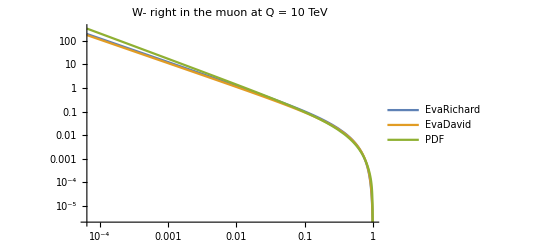

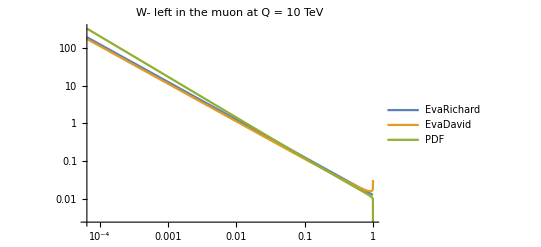

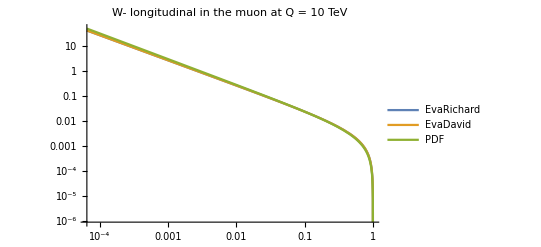

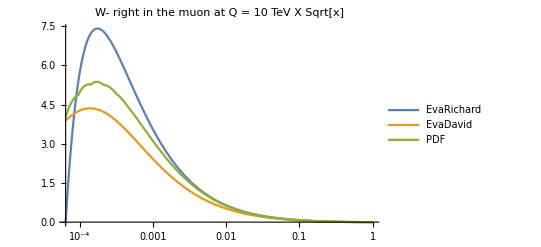

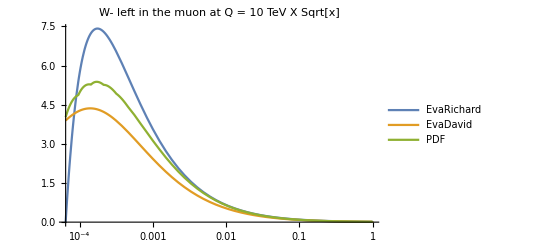

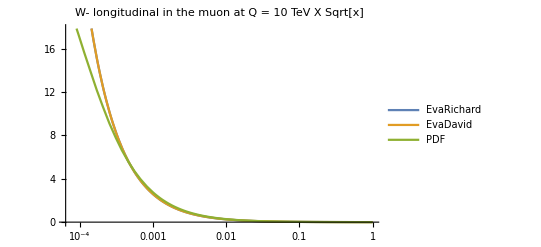

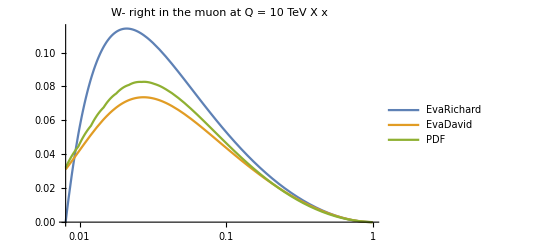

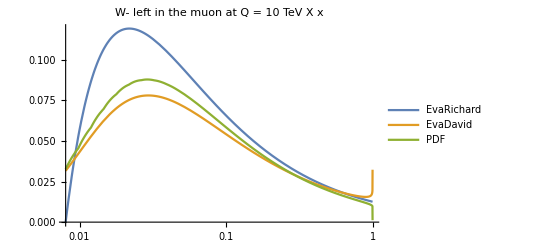

```mathematica
Q=10000


LogLogPlot[{μEVApart[Wmp,Q ,x],μEVApartv2[Wmp,Q ,x],μPDFpart[Wmp,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV"]
LogLogPlot[{μEVApart[Wmm,Q ,x],μEVApartv2[Wmm,Q ,x],μPDFpart[Wmm,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV"]
LogLogPlot[{μEVApart[WmL,Q ,x],μEVApartv2[WmL,Q ,x],μPDFpart[WmL,Q][x]},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV"]

LogLinearPlot[{μEVApart[Wmp,Q Sqrt[x],x],μEVApartv2[Wmp,Q Sqrt[x],x],μPDFpart[Wmp,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]
LogLinearPlot[{μEVApart[Wmm,Q Sqrt[x],x],μEVApartv2[Wmm,Q Sqrt[x],x],μPDFpart[Wmm,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]
LogLinearPlot[{μEVApart[WmL,Q Sqrt[x],x],μEVApartv2[WmL,Q Sqrt[x],x],μPDFpart[WmL,Q Sqrt[x]][x]},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]


LogLinearPlot[{μEVApart[Wmp,Q x,x],μEVApartv2[Wmp,Q x,x],μPDFpart[Wmp,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
LogLinearPlot[{μEVApart[Wmm,Q x,x],μEVApartv2[Wmm,Q x,x],μPDFpart[Wmm,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- left in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
LogLinearPlot[{μEVApart[WmL,Q x,x],μEVApartv2[WmL,Q x,x],μPDFpart[WmL,Q x][x]},{x,(MW/Q)^1,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"W- longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
```

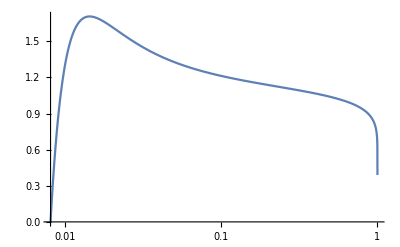

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q x ,x]/μEVApartv2[Wmp,Q x,x]},{x,(MW/Q),1}]
```

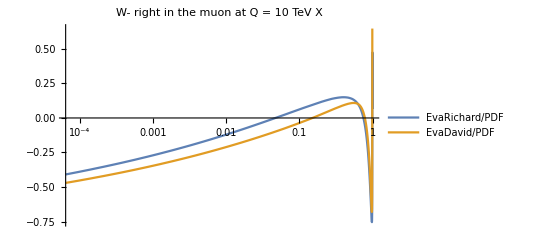

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q ][x]-1,μEVApartv2[Wmp,Q ,x]/μPDFpart[Wmp,Q ][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard/PDF","EvaDavid/PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X "]
```

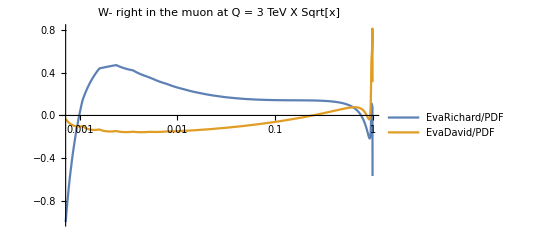

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q Sqrt[x],x]/μPDFpart[Wmp,Q Sqrt[x]][x]-1,μEVApartv2[Wmp,Q Sqrt[x],x]/μPDFpart[Wmp,Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard/PDF","EvaDavid/PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]
```

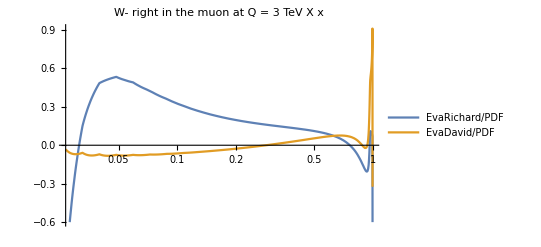

```mathematica
LogLinearPlot[{μEVApart[Wmp,Q x,x]/μPDFpart[Wmp,Q x][x]-1,μEVApartv2[Wmp,Q x,x]/μPDFpart[Wmp,Q x][x]-1},{x,(MW/Q)^1,1},PlotLegends->{"EvaRichard/PDF","EvaDavid/PDF"},PlotLabel->"W- right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
```

```mathematica
(*μLEVApartv2[Wmp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesW(*2.7 a*)*)
```

```mathematica
LogLogPlot[{μLEVApart[Wmp,Q ,x],μLEVApart[Wmp,Q ,x]/2,μLEVApartv2[Wmp,Q,x],μLEVApartv2[Wmp,Q,x]/2,μPDFpart[Wmp,Q][x]},{x,0.001,1},PlotLegends->{"EvaRichard μL ","EvaRichard/2 μL ","EvaRichard μL scale as David","EvaRichard/2 μL scale as David ","PDF for μ not μL"},PlotLabel->"W- right in the muon"]
LogLinearPlot[{μLEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q][x]-1,μLEVApart[Wmp,Q ,x]/2/μPDFpart[Wmp,Q][x]-1,μLEVApartv2[Wmp,Q,x]/μPDFpart[Wmp,Q][x]-1,μLEVApartv2[Wmp,Q,x]/2/μPDFpart[Wmp,Q][x]-1,μPDFpart[Wmp,Q][x]/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5},PlotLegends->{"EvaRichard μL ","EvaRichard/2 μL ","EvaRichard μL scale as David","EvaRichard/2 μL scale as David ","PDF for μ not μL"},PlotLabel->"W- right in the muon: ratio with PDF for μ not μL"]

(*LogLogPlot[{ μEVApart[Wmp,Q ,x],μPDFpart[Wmp,Q][x]},{x,0.001,0.5}]
LogLinearPlot[{ μEVApart[Wmp,Q ,x]/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{ (μEVApart[Wmp,Sqrt[Q ^2+MW^2(1-x)]/Sqrt[(1-x) /Exp[Q^2/(Q^2+(1-x)MW^2)]],x])/μPDFpart[Wmp,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{μEVApart[Wmm,Q ,x]/μPDFpart[Wmm,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{(μEVApart[Wmp,Q ,x]+μEVApart[Wmm,Q ,x])/μPDFpart[WmT,Q][x]-1},{x,0.001,0.5}]
LogLinearPlot[{μEVApart[WmL,Q ,x]/μPDFpart[WmL,Q][x]-1},{x,0.001,0.5}]*)
```

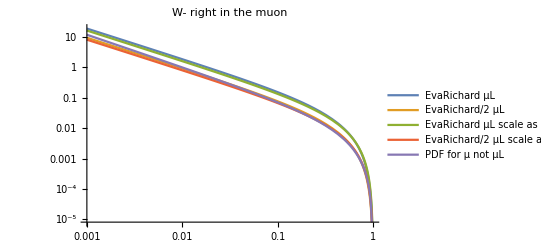

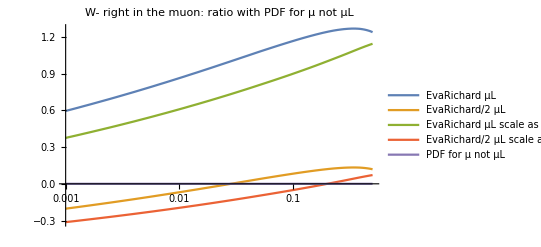

```mathematica
(*Plot di Debug*)
```

```mathematica
(-1/2)-(-1)*sw^2
```

-0.276987

```mathematica
(*!!!!!!!  !!!!!!!!*)
```

```mathematica
rulesZfL={(*gV->1/2*(-1/2)-(-1)sw^2,*)gV->1,gL->(-1/2)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}
rulesZfR={(*gV->1/2*(0)-(-1)sw^2,*)gV->1,gL->(0)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}

μLEVApart[Zp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesZfL(*2.7 a*)
μLEVApart[Zm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2]/.rulesZfL (*2.7 b*)
μLEVApart[ZL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesZfL(*2.7 c*)

μREVApart[Zp,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 /(2x)Log[Q^2/MV^2] /.rulesZfR(*2.7 d*)
μREVApart[Zm,Q_,x_]:=(gR^2/gL^2) gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)Log[Q^2/MV^2] /.rulesZfR(*2.7 e*)
μREVApart[ZL,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 (1-x)/(x) /.rulesZfR(*2.7 f*)

μEVApart[Zp,Q_,x_]:=(μLEVApart[Zp,Q,x]+μREVApart[Zp,Q,x])/2




μEVApart[Zm,Q_,x_]:=(μLEVApart[Zm,Q,x]+μREVApart[Zm,Q,x])/2



μEVApart[ZL,Q_,x_]:=(μLEVApart[ZL,Q,x]+μREVApart[ZL,Q,x])/2



(*Scale as LEPDF EVA*)

rulesZfL={(*gV->1/2*(-1/2)-(-1)sw^2,*)gV->1,gL->(-1/2)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}
rulesZfR={(*gV->1/2*(0)-(-1)sw^2,*)gV->1,gL->(0)-(-1)sw^2,gR->-(-1)sw^2,gt->g/cw,MV->MZ}

μLEVApartv2[Zp,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfL(*2.7 a*)
μLEVApartv2[Zm,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2)) /.rulesZfL (*2.7 b*)
μLEVApartv2[ZL,Q_,x_]:=gt^2gV^2/4/Pi^2gL^2 (1-x)/(x)/.rulesZfL(*2.7 c*)

μREVApartv2[Zp,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 /(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfR(*2.7 d*)
μREVApartv2[Zm,Q_,x_]:=(gR^2/gL^2) gt^2gV^2/4/Pi^2gL^2 (1-x)^2/(2x)(Log[(Q^2+(1-x)MV^2)/(MV^2*(1-x))]-Q^2/(Q^2+(1-x)MV^2))  /.rulesZfR(*2.7 e*)
μREVApartv2[ZL,Q_,x_]:=(gR^2/gL^2)gt^2gV^2/4/Pi^2gL^2 (1-x)/(x) /.rulesZfR(*2.7 f*)

μEVApartv2[Zp,Q_,x_]:=(μLEVApartv2[Zp,Q,x]+μREVApartv2[Zp,Q,x])/2




μEVApartv2[Zm,Q_,x_]:=(μLEVApartv2[Zm,Q,x]+μREVApartv2[Zm,Q,x])/2



μEVApartv2[ZL,Q_,x_]:=(μLEVApartv2[ZL,Q,x]+μREVApartv2[ZL,Q,x])/2






μEVApart[Zp,Q,x]
```

{gV→1,gL→-0.276987,gR→0.223013,gt→0.727566,MV→91.1876}

{gV→1,gL→0.223013,gR→0.223013,gt→0.727566,MV→91.1876}

{gV→1,gL→-0.276987,gR→0.223013,gt→0.727566,MV→91.1876}

{gV→1,gL→0.223013,gR→0.223013,gt→0.727566,MV→91.1876}

1/2 (0.0023297/x+(0.00359383 (1-x)^2)/x)

3000

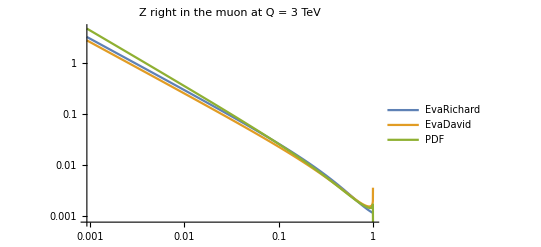

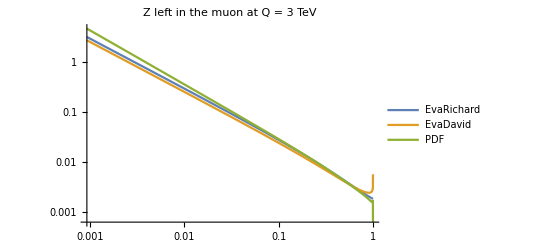

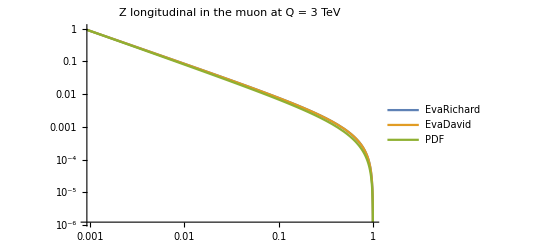

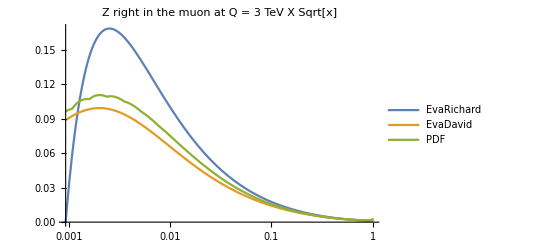

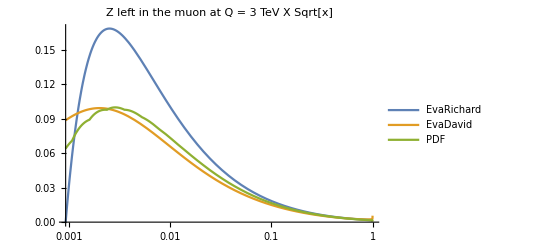

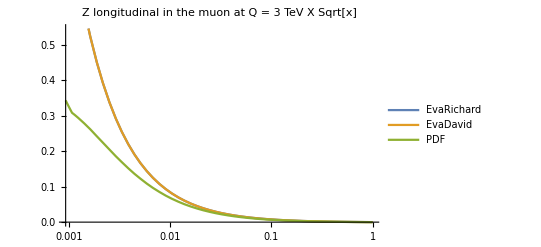

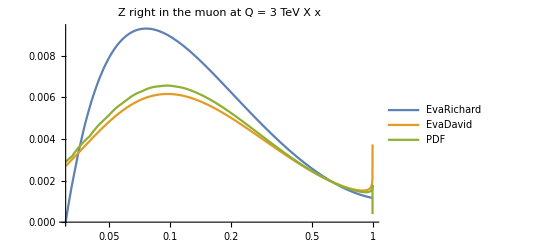

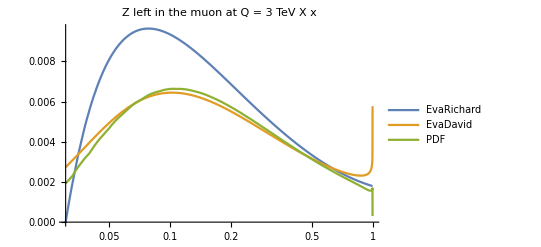

```mathematica
Q=3000

LogLogPlot[{μEVApart[Zp,Q ,x],μEVApartv2[Zp,Q ,x],μPDFpart[Zp,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV"]
LogLogPlot[{μEVApart[Zm,Q ,x],μEVApartv2[Zm,Q ,x],μPDFpart[Zm,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV"]
LogLogPlot[{μEVApart[ZL,Q ,x],μEVApartv2[ZL,Q ,x],μPDFpart[ZL,Q][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV"]


LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x],μEVApartv2[Zp,Q Sqrt[x],x],μPDFpart[Zp,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]
LogLinearPlot[{μEVApart[Zm,Q Sqrt[x],x],μEVApartv2[Zm,Q Sqrt[x],x],μPDFpart[Zm,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]
LogLinearPlot[{μEVApart[ZL,Q Sqrt[x],x],μEVApartv2[ZL,Q Sqrt[x],x],μPDFpart[ZL,Q Sqrt[x]][x]},{x,(MZ/Q)^2,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]


LogLinearPlot[{μEVApart[Zp,Q x,x],μEVApartv2[Zp,Q x,x],μPDFpart[Zp,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
LogLinearPlot[{μEVApart[Zm,Q x,x],μEVApartv2[Zm,Q x,x],μPDFpart[Zm,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z left in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
LogLinearPlot[{μEVApart[ZL,Q x,x],μEVApartv2[ZL,Q x,x],μPDFpart[ZL,Q x][x]},{x,(MZ/Q)^1,1},PlotLegends->{"EvaRichard","EvaDavid","PDF"},PlotLabel->"Z longitudinal in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
```

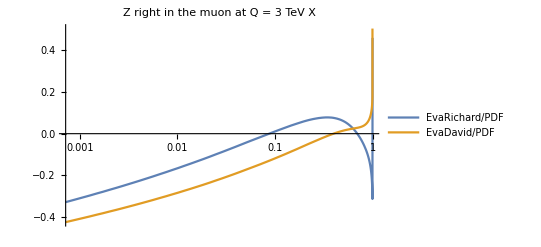

```mathematica
LogLinearPlot[{μEVApart[Zp,Q ,x]/μPDFpart[Zp,Q ][x]-1,μEVApartv2[Zp,Q ,x]/μPDFpart[Zp,Q ][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard/PDF","EvaDavid/PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X "]
```

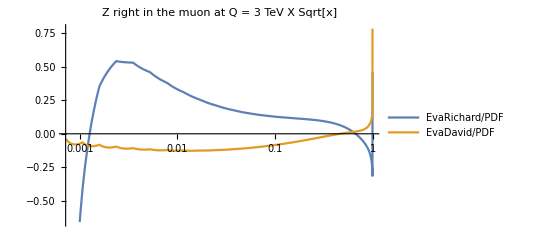

```mathematica
LogLinearPlot[{μEVApart[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1,μEVApartv2[Zp,Q Sqrt[x],x]/μPDFpart[Zp,Q Sqrt[x]][x]-1},{x,(MW/Q)^2,1},PlotLegends->{"EvaRichard/PDF","EvaDavid/PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X Sqrt[x]"]
```

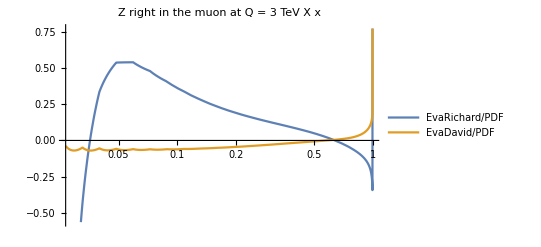

```mathematica
LogLinearPlot[{μEVApart[Zp,Q x,x]/μPDFpart[Zp,Q x][x]-1,μEVApartv2[Zp,Q x,x]/μPDFpart[Zp,Q x][x]-1},{x,(MW/Q)^1,1},PlotLegends->{"EvaRichard/PDF","EvaDavid/PDF"},PlotLabel->"Z right in the muon at Q = "<>ToString[Q/1000]<>" TeV X x"]
```

```mathematica
Lμmμp[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μPDFpart[part1,mμμ/2][x]μbPDFpart[part2,mμμ/2][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]
```

```mathematica
LμmμpNpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),Lμmμp[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0]},{i,1,Npoints}]
```

```mathematica
LμmμpNpoints[μL,μLb,1000,3000,20]
```

{{1000,0.0105059},{21000/19,0.0108984},{23000/19,0.011387},{25000/19,0.0119855},{27000/19,0.0127033},{29000/19,0.0135726},{31000/19,0.0146226},{33000/19,0.0158933},{35000/19,0.0174498},{37000/19,0.0193695},{39000/19,0.0217846},{41000/19,0.0248558},{43000/19,0.0288785},{45000/19,0.034278},{47000/19,0.0418631},{49000/19,0.0531713},{51000/19,0.071692},{53000/19,0.107493},{55000/19,0.207777},{3000,0.}}

Parton luminosity for a μ- <> μ+ collider as function of the partonic  invariant mass m, which also fixes the PDF factorization scale as m/2.

```mathematica
μPDFpart[WmT,500/2][0.1]
```

0.0195723

```mathematica
Lμmμp[WmT,WpT,400,3000]
```

0.000536622

```mathematica
bins=20
Stot=10000
minM=200
```

20

10000

200

```mathematica
joinedoption=True
```

True

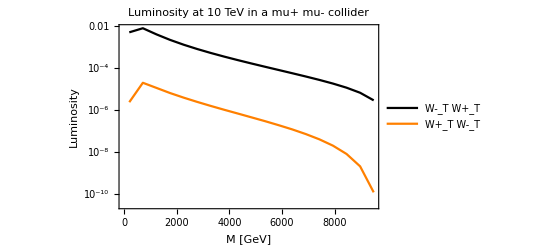

```mathematica
ListLogPlot[{LμmμpNpoints[WmT,WpT,minM,Stot,bins],LμmμpNpoints[WpT,WmT,minM,Stot,bins]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"M [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W+_T W-_T","W-_T","W-_L","W+_T","W+_L","Z_T","Z_L"},PlotLabel->"Luminosity at "<>ToString[Stot/1000]<>" TeV in a mu+ mu- collider",Joined->joinedoption]
```

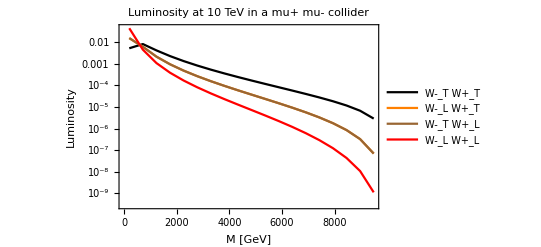

```mathematica
ListLogPlot[{LμmμpNpoints[WmT,WpT,minM,Stot,bins],LμmμpNpoints[WmL,WpT,minM,Stot,bins],LμmμpNpoints[WmT,WpL,minM,Stot,bins],LμmμpNpoints[WmL,WpL,minM,Stot,bins]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"M [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W-_L W+_T","W-_T W+_L","W-_L W+_L"},PlotLabel->"Luminosity at "<>ToString[Stot/1000]<>" TeV in a mu+ mu- collider",Joined->joinedoption]
```

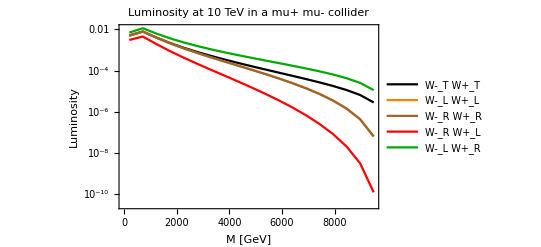

```mathematica
ListLogPlot[{LμmμpNpoints[WmT,WpT,minM,Stot,bins],LμmμpNpoints[Wmm,Wpm,minM,Stot,bins],LμmμpNpoints[Wmp,Wpp,minM,Stot,bins],LμmμpNpoints[Wmp,Wpm,minM,Stot,bins],LμmμpNpoints[Wmm,Wpp,minM,Stot,bins]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"M [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"W-_T W+_T","W-_L W+_L","W-_R W+_R","W-_R W+_L","W-_L W+_R"},PlotLabel->"Luminosity at "<>ToString[Stot/1000]<>" TeV in a mu+ mu- collider",Joined->joinedoption]
```

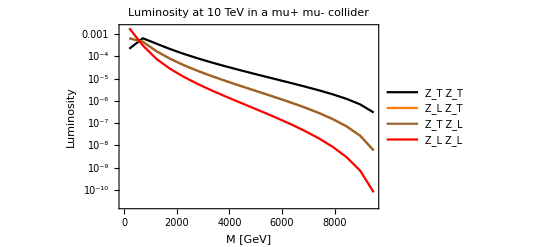

```mathematica
ListLogPlot[{LμmμpNpoints[ZT,ZT,minM,Stot,bins],LμmμpNpoints[ZL,ZT,minM,Stot,bins],LμmμpNpoints[ZT,ZL,minM,Stot,bins],LμmμpNpoints[ZL,ZL,minM,Stot,bins]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"M [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"Z_T Z_T","Z_L Z_T","Z_T Z_L","Z_L Z_L"},PlotLabel->"Luminosity at "<>ToString[Stot/1000]<>" TeV in a mu+ mu- collider",Joined->joinedoption]
```

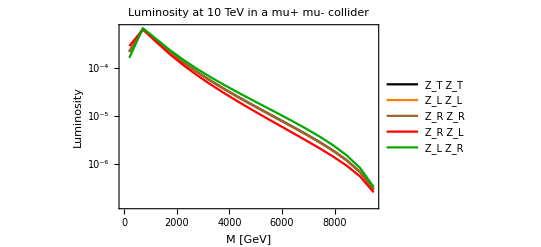

```mathematica
ListLogPlot[{LμmμpNpoints[ZT,ZT,minM,Stot,bins],LμmμpNpoints[Zm,Zm,minM,Stot,bins],LμmμpNpoints[Zp,Zp,minM,Stot,bins],LμmμpNpoints[Zp,Zm,minM,Stot,bins],LμmμpNpoints[Zm,Zp,minM,Stot,bins]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"M [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"Z_T Z_T","Z_L Z_L","Z_R Z_R","Z_R Z_L","Z_L Z_R"},PlotLabel->"Luminosity at "<>ToString[Stot/1000]<>" TeV in a mu+ mu- collider",Joined->joinedoption]
```

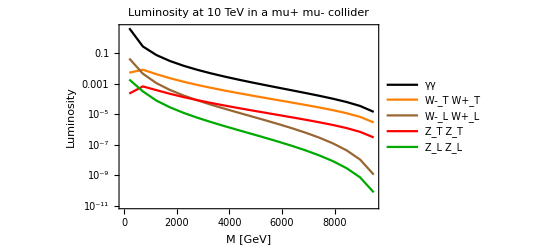

```mathematica
ListLogPlot[{LμmμpNpoints[γ,γ,minM,Stot,bins],LμmμpNpoints[WmT,WpT,minM,Stot,bins],LμmμpNpoints[WmL,WpL,minM,Stot,bins],LμmμpNpoints[ZT,ZT,minM,Stot,bins],LμmμpNpoints[ZL,ZL,minM,Stot,bins]},PlotStyle->{Black,Orange,Brown,Red,Darker[Green],Cyan,Gray,Purple,Blue,Magenta}(*,PlotRange->{{0.00099,1},{0.001,100}}*),Frame->True,FrameLabel->{"M [GeV]","Luminosity"},RotateLabel->True,BaseStyle->Directive[17,FontFamily->"Times"],FrameStyle->Directive[Black],PlotLegends->{"γγ","W-_T W+_T","W-_L W+_L","Z_T Z_T","Z_L Z_L"},PlotLabel->"Luminosity at "<>ToString[Stot/1000]<>" TeV in a mu+ mu- collider",Joined->joinedoption]
```

```mathematica
(*

μbEVA has to be defined before



LμmμpEVA[part1_,part2_,mμμ_,sqrts0_]:=NIntegrate[1/x μEVApart[part1,mμμ/2][x]μbEVApart[part2,mμμ/2][mμμ^2/(x sqrts0^2)],{x,mμμ^2/sqrts0^2,1},AccuracyGoal->8,MaxRecursion->100]

LμmμpEVANpoints[part1_,part2_,mμμ_,sqrts0_,Npoints_]:=Table[{mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),LμmμpEVA[part1,part2,mμμ+(i-1)*(sqrts0-mμμ)/(Npoints-1),sqrts0]},{i,1,Npoints}]*)
```